```mathematica
ClearAll["Global`*"]
```

```mathematica
s0={{1.321831311995715,139.50193996500002},{1.777198697495715,135.53781773342862},{1.9394716652000004,137.3304999494286},{2.1769503464528577,136.70700505600004}}
```

{{1.32183,139.502},{1.7772,135.538},{1.93947,137.33},{2.17695,136.707}}

```mathematica
s5={{1.3384336533187002,138.92059118720002},{1.8309841931620001,134.53625385520002},{2.041411750949,125.45823807340001},{2.4807026393260005,130.94196403330002}}
```

{{1.33843,138.921},{1.83098,134.536},{2.04141,125.458},{2.4807,130.942}}

```mathematica
s11={{2.015948142545,114.95426829700001} ,{2.4663530361300006,115.58141286840001},{ 2.856645804237001,114.81478809430003},{ 3.0686094655820013,118.13289369870004}}
```

{{2.01595,114.954},{2.46635,115.581},{2.85665,114.815},{3.06861,118.133}}

```mathematica
s17={{2.191056271616,107.62978975850002} ,{2.9348488390400007,100.83666103307003},{ 3.329791693112,102.83541406403} ,{3.7772744415450004,103.45938233500004}}
```

{{2.19106,107.63},{2.93485,100.837},{3.32979,102.835},{3.77727,103.459}}

```mathematica
funkt=c+m x
```

c+m x

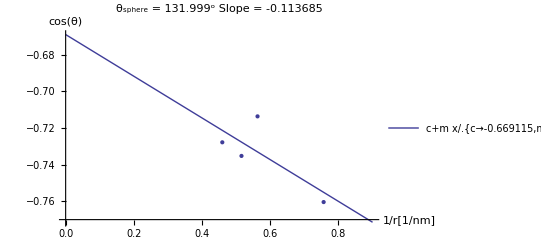

```mathematica
s0tr=Table[{1/s0[[i,1]],Cos[s0[[i,2]]/180 Pi]},{i,1,4}];
fit0=FindFit[s0tr,funkt,{c,m},x];
Show[Plot[{funkt/.fit0},{x,0,0.9},PlotLegends->LineLegend["Expressions"]],ListPlot[{s0tr}],AxesLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"θ_sphere = "<>ToString[ArcCos[c/.fit0]180/Pi]<>"^o  "<>"Slope = "<>ToString[m/.fit0]]
```

```mathematica
s5tr=Table[{1/s5[[i,1]],Cos[s5[[i,2]]/180 Pi]},{i,1,4}];
fit5=FindFit[s5tr,funkt,{c,m},x];
```

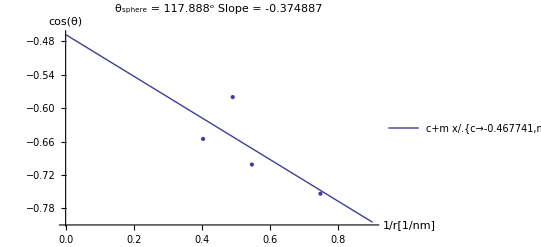

```mathematica
Show[Plot[{funkt/.fit5},{x,0,0.9},PlotLegends->LineLegend["Expressions"]],ListPlot[{s5tr}],AxesLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"θ_sphere = "<>ToString[ArcCos[c/.fit5]180/Pi]<>"^o  "<>"Slope = "<>ToString[m/.fit5]]
```

```mathematica
s11tr=Table[{1/s11[[i,1]],Cos[s11[[i,2]]/180 Pi]},{i,1,4}];
fit11=FindFit[s11tr,funkt,{c,m},x];
```

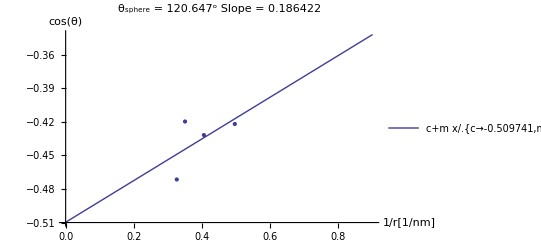

```mathematica
Show[Plot[{funkt/.fit11},{x,0,0.9},PlotLegends->LineLegend["Expressions"]],ListPlot[{s11tr}],AxesLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"θ_sphere = "<>ToString[ArcCos[c/.fit11]180/Pi]<>"^o  "<>"Slope = "<>ToString[m/.fit11]]
```

```mathematica
s17tr=Table[{1/s17[[i,1]],Cos[s11[[i,2]]/180 Pi]},{i,1,4}];
fit17=FindFit[s17tr,funkt,{c,m},x];
```

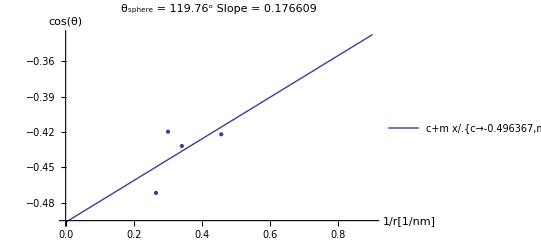

```mathematica
Show[Plot[{funkt/.fit17},{x,0,0.9},PlotLegends->LineLegend["Expressions"]],ListPlot[{s17tr}],AxesLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"θ_sphere = "<>ToString[ArcCos[c/.fit17]180/Pi]<>"^o  "<>"Slope = "<>ToString[m/.fit17]]
```

{{0,131.999},{5,117.888},{11,120.647},{17,119.76},{66,0}}

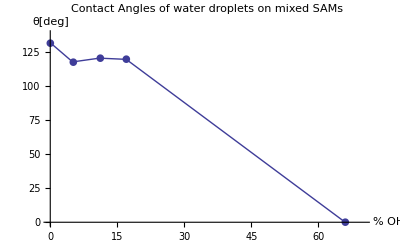

```mathematica
angles={{0,131.999},{5,117.888},{11,120.647},{17,119.76},{66,0}}
Show[ListLinePlot[angles],ListPlot[angles,PlotMarkers->{●,10}],PlotRange->{{0,70},{0,138}},AxesLabel->{"% OH","θ[deg]"},PlotLabel->"Contact Angles of water droplets on mixed SAMs"]
```

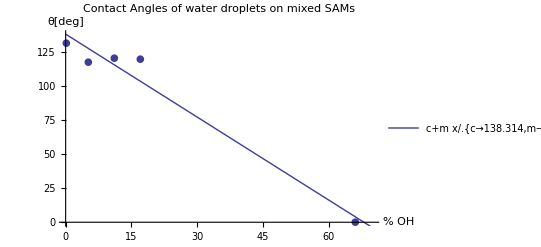

```mathematica
fitangles=FindFit[angles,funkt,{c,m},x];
Show[Plot[{funkt/.fitangles},{x,0,70},PlotLegends->LineLegend["Expressions"]],ListPlot[angles,PlotMarkers->{●,10}],PlotRange->{{0,70},{0,138}},AxesLabel->{"% OH","θ[deg]"},PlotLabel->"Contact Angles of water droplets on mixed SAMs"]
```

```mathematica
c1=138.314
m1=-2.03312
-c1/m1
```

138.314

-2.03312

68.0304

{{0,131.999},{5,117.888},{11,120.647},{17,119.76}}

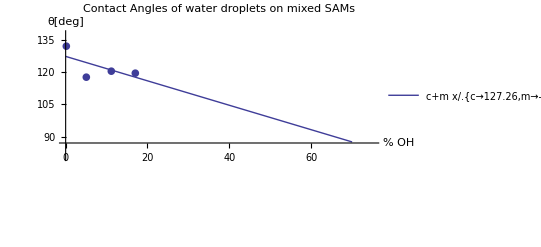

```mathematica
angles2={{0,131.999},{5,117.888},{11,120.647},{17,119.76}}
fitangles2=FindFit[angles2,funkt,{c,m},x];
Show[Plot[{funkt/.fitangles2},{x,0,70},PlotLegends->LineLegend["Expressions"]],ListPlot[angles,PlotMarkers->{●,10}],PlotRange->{{0,75},{80,138}},AxesLabel->{"% OH","θ[deg]"},PlotLabel->"Contact Angles of water droplets on mixed SAMs"]
```

```mathematica
c=127.26;
 m=-0.56804;
-c/m
```

224.034

{-0.113685,-0.374887,0.186422,0.176609,0}

{5.99119,19.7565,-9.82444,-9.30728,0.}

{0,5,11,17,66}

{{0,5.99119},{5,19.7565},{11,-9.82444},{17,-9.30728},{66,0.}}

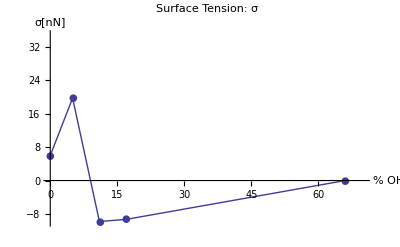

```mathematica
slopes={-0.11368477999599405,-0.3748866453975821,0.18642193528655776,0.17660871843271828,0}
tensions=slopes*(-52.7)
OH={0,5,11,17,66}
sigmas=Thread[{OH,tensions}]
Show[ListLinePlot[sigmas],ListPlot[sigmas,PlotMarkers->{●,10}],PlotRange->{{0,70},{-10,35}},AxesLabel->{"% OH","σ[nN]"},PlotLabel->"Surface Tension: σ"]
```

{131.999,117.888,120.647,119.76,0}

{2.30382,2.05753,2.10569,2.09021,0}

{{5.99119,2.30382},{19.7565,2.05753},{-9.82444,2.10569},{-9.30728,2.09021},{0.,0}}

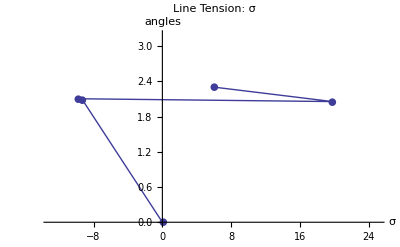

```mathematica
angles3=angles[[All,2]]
anglesrads=(angles3/360)*2*Pi
angletension=Thread[{tensions,anglesrads}]
Show[ListLinePlot[angletension],ListPlot[angletension,PlotMarkers->{●,10}],PlotRange->{{-13,25},{0,3.2}},AxesLabel->{"σ","angles"},PlotLabel->"Line Tension: σ"]
```